```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[20]]&];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

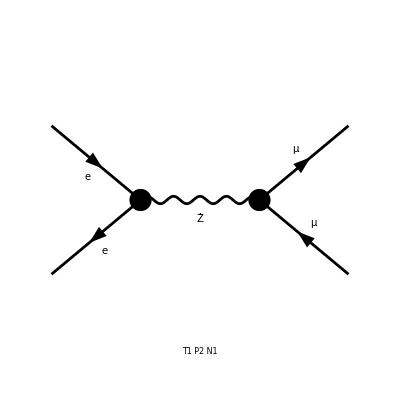

```mathematica
Paint[fieldsBorn];
```

```mathematica
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,Boxes,WFCorrections}];
topologies1L=topologies1L[[0]][topologies1L[[1]]];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[20]]&];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

in total: 14 Particles amplitudes

Electron Mass to zero

```mathematica
ampBorn=ampBorn/.ME->0;
amp1L=amp1L/.ME->0;
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

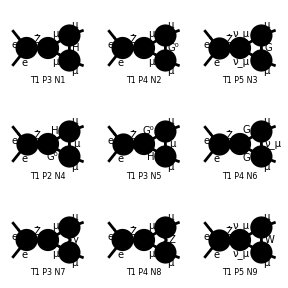

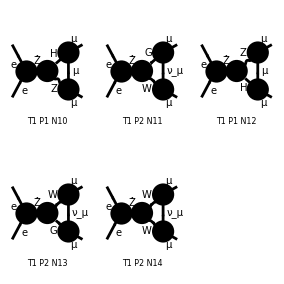

```mathematica
Paint[fields1L];
```

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/feynArts_amplitudes/BornAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/feynArts_amplitudes/OneLoopAmplitudes.m

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
smBorn=AmpSquare[myAmpBorn,myAmpBorn]//Simplify;
```

```mathematica
smBorn/.parameterReplace/.{I3l1->-1/2,Ql1->-1}
```

{1/(4 (mz^2-s)^2)EL^4 (4 mm^4 (SW^2/CW^2+((-1/2+SW^2)^2)/(CW^2 SW^2)) ((Ql2^2 SW^2)/CW^2+((I3l2-Ql2 SW^2)^2)/(CW^2 SW^2))+(-2+d) s^2 ((SW^2 (((-2+d) Ql2^2 SW^2)/CW^2-((-4+d) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)))/CW^2+((-1/2+SW^2)^2 (-((-4+d) Ql2^2 SW^2)/CW^2+((-2+d) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)))/(CW^2 SW^2))+4 (SW^2/CW^2+((-1/2+SW^2)^2)/(CW^2 SW^2)) ((Ql2^2 SW^2)/CW^2+((I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)) t^2-2 mm^2 ((-2+d) s ((SW^2 (((-2+d) Ql2^2 SW^2)/CW^2-((-4+d) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)))/CW^2+((-1/2+SW^2)^2 (-((-4+d) Ql2^2 SW^2)/CW^2+((-2+d) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)))/(CW^2 SW^2))+4 (SW^2/CW^2+((-1/2+SW^2)^2)/(CW^2 SW^2)) ((Ql2^2 SW^2)/CW^2+((I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)) t)+2 s (-(2 (-2+d) mm^2 Ql2 (I3l2-Ql2 SW^2) (SW^2/CW^2+((-1/2+SW^2)^2)/(CW^2 SW^2)))/CW^2+(SW^2 (((8-5 d+d^2) Ql2^2 SW^2)/CW^2-((4-5 d+d^2) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)) t)/CW^2+((-1/2+SW^2)^2 (-((4-5 d+d^2) Ql2^2 SW^2)/CW^2+((8-5 d+d^2) (I3l2-Ql2 SW^2)^2)/(CW^2 SW^2)) t)/(CW^2 SW^2)))}

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn];
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles//interferences/Contribution_14_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,14},{j,1}]
```

ABISS: Integral family {{A0, {mh, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_1_1.m.

ABISS: Integral family {{A0, {mz, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_2_1.m.

ABISS: Integral family {{C0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_3_1.m.

ABISS: Integral family {{D0, {mm, mh, mz}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_4_1.m.

ABISS: Integral family {{D0, {mm, mz, mh}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_5_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_6_1.m.

ABISS: Integral family {{B0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_7_1.m.

ABISS: Integral family {{A0, {mz, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_8_1.m.

ABISS: Integral family {{C0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_9_1.m.

ABISS: Integral family {{D0, {mm, mh, mz}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_10_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_11_1.m.

ABISS: Integral family {{D0, {mm, mz, mh}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_12_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_13_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/interferences/Contribution_14_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,14},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_14_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[C0,{m1},0,0,1,0]→0,userIntegral[C0,{m1},0,1,0,0]→0,userIntegral[B0,{m1},1,0,0,0]→0,userIntegral[A0,{m1,m2},1,0,1,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[A0,{m1,m2},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[A0,{m1,m2},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)+2 m2^2 t-s t+mm^2 (2 m1^2+2 m2^2+2 t)) userIntegral[A0,{m1,m2},1,1,1,0])/(4 mm^2-s),userIntegral[A0,{m1,m2},1,-1,1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-56+24 d) m2^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((32-16 d) s+(48-16 d) t))) userIntegral[A0,{m1,m2},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+(2-d) m2^2 s t^2+mm^6 ((-20+8 d) m1^2+(-12+8 d) m2^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+m2^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+m2^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) m2^2+(8-8 d) t)+m2^4 (4 s t+(-4+4 d) t^2)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) m2^4+(-4+4 d) s t+(-4+4 d) t^2+m2^2 ((-24+8 d) m1^2+16 t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+m2^2 ((8-4 d) s t^2+m1^2 (-4 d s t+(8-8 d) t^2))+mm^2 ((-24+8 d) m2^4 t+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+m2^2 (-4 d s t+(-24+8 d) t^2+m1^2 ((8-4 d) s+16 t)))) userIntegral[A0,{m1,m2},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[A0,{m1,m2},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},0,0,1,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[A0,{m1,m2},0,1,1,-1]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (2 m2^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[A0,{m1,m2},-1,1,1,0]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (-2 m1^2+2 m2^2+2 mm^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[C0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,1,1,-1]→((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[C0,{m1},0,1,1,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)-s t+mm^2 (2 m1^2+2 t)) userIntegral[C0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[C0,{m1},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,1,-2]→((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+mm^6 ((-20+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t))) userIntegral[C0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) s t+(-4+4 d) t^2+m1^2 ((-4+4 d) s+(-16+16 d) t))+mm^2 ((8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2))) userIntegral[C0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[C0,{m1},1,1,0,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[C0,{m1},1,1,0,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,-1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},0,1,1,-1]→-1/2 s userIntegral[C0,{m1},0,1,1,0],userIntegral[C0,{m1},-1,1,1,0]→1/2 (-2 m1^2+2 mm^2-s) userIntegral[C0,{m1},0,1,1,0],userIntegral[D0,{m1,m2,m3},1,1,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[D0,{m1,m2,m3},0,1,1,0])/(4 mm^2-s)+((mm^2+t) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(4 mm^2-s)+1/(4 mm^2-s)(-2 mm^4+m1^2 (-s-2 t)+m2^2 t+m3^2 t-s t+mm^2 (2 m1^2+m2^2+m3^2+2 t)) userIntegral[D0,{m1,m2,m3},1,1,1,0],userIntegral[D0,{m1,m2,m3},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+(s userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((m1^2 s-m3^2 s+mm^2 (-2 m2^2+2 m3^2+s)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((mm^2-t) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((-mm^4-m1^2 t+m3^2 t+mm^2 (m1^2+m3^2+t)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(8 mm^4-2 mm^2 s)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+((mm^8 (-8 m2^2+8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m2^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m3^2 ((-4+2 d) s-16 t)+8 s t+m2^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m2^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m3^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m3^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m2^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(8 mm^4-2 mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-28+12 d) m2^2+(-28+12 d) m3^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m3^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((16-8 d) s+(24-8 d) t)+m3^2 ((16-8 d) s+(24-8 d) t))) userIntegral[D0,{m1,m2,m3},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^8 (8 m2^2-8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m3^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m2^2 ((-4+2 d) s-16 t)+8 s t+m3^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m3^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m2^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m2^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m3^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[D0,{m1,m2,m3},1,0,1,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+(((-4+4 d) mm^8 s+(-2+d) m2^4 s t^2+(-2+d) m3^4 s t^2+(-2+d) s^3 t^2+mm^6 (4 m2^4+4 m3^4+(8-8 d) m1^2 s+(4-4 d) m2^2 s+m3^2 (-8 m2^2+(4-4 d) s)+(8-8 d) s t)+m1^4 ((-2+d) s^3+(-4+4 d) s^2 t+(-4+4 d) s t^2)+m1^2 (2 d s^3 t+(-4+4 d) s^2 t^2)+m2^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2))+m3^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2)+m2^2 (4 s^2 t+2 d s t^2))+mm^4 ((-4+4 d) m1^4 s+m2^4 ((-2+d) s-8 t)+m3^4 ((-2+d) s-8 t)+(-4+4 d) s^2 t+(-4+4 d) s t^2+m2^2 ((-12+4 d) m1^2 s+8 s t)+m1^2 ((-4+4 d) s^2+(-16+16 d) s t)+m3^2 ((-12+4 d) m1^2 s+8 s t+m2^2 (2 d s+16 t)))+mm^2 ((8-4 d) s^2 t^2+m1^4 ((8-4 d) s^2+(8-8 d) s t)+m2^4 (2 d s t+4 t^2)+m3^4 (2 d s t+4 t^2)+m1^2 (-8 d s^2 t+(8-8 d) s t^2)+m2^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t))+m3^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t)+m2^2 ((-24+4 d) s t-8 t^2)))) userIntegral[D0,{m1,m2,m3},1,1,1,0])/((-32+16 d) mm^4 s+(16-8 d) mm^2 s^2+(-2+d) s^3),userIntegral[D0,{m1,m2,m3},1,1,0,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[D0,{m1,m2,m3},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[D0,{m1,m2,m3},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 (2 m2^2-2 m3^2+s)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},0,1,1,-1]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (m2^2+m3^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[D0,{m1,m2,m3},0,1,0,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[D0,{m1,m2,m3},-1,1,1,0]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (-2 m1^2+m2^2+m3^2+2 mm^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[B0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[B0,{m1},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[B0,{m1},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+2 m1^2 t-s t+mm^2 (2 m1^2+2 t)) userIntegral[B0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[B0,{m1},1,-1,1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-56+24 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((32-16 d) s+(48-16 d) t))) userIntegral[B0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((12-8 d) mm^8+(2-d) m1^2 s t^2+mm^6 ((-12+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(8-4 d) m1^2 s t^2+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 (4 s t+(-4+4 d) t^2)+mm^4 ((-4+4 d) m1^4+16 m1^2 t+(-4+4 d) s t+(-4+4 d) t^2)+mm^2 ((-24+8 d) m1^4 t+(8-4 d) s t^2+m1^2 (-4 d s t+(-24+8 d) t^2))) userIntegral[B0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[B0,{m1},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,-1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},0,0,1,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},0,1,1,-1]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2-s) userIntegral[B0,{m1},0,1,1,0],userIntegral[B0,{m1},0,1,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},-1,1,1,0]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 mm^2-s) userIntegral[B0,{m1},0,1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,14},{j,1}]
```

```mathematica
Transliterate
```

abck.12.14

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,14}]
```

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
minorReplace1={gAl->-Ql,gAu->-Qu,gAd->-Qd};
minorReplace2={gZlL->(I3l-Ql*sw^2)/(cw*sw),gZlR->(-Ql*sw^2)/(cw*sw),gZNL->(I3N)/(cw*sw),gZuL->(I3u-(Qu*sw^2))/(cw*sw),gZuR->(-Qu*sw^2)/(cw*sw),gZdL->(I3d-(Qd*sw^2))/(cw*sw),gZdR->(-Qd*sw^2)/(cw*sw)};
```

```mathematica
coefficients=Plus@@diagramCoefficients //Simplify
```

diagramCoefficients

```mathematica
Length[coefficients]
```

34

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m")
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
masters=DeleteDuplicates[masters]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Length[masters]
```

34

```mathematica
userIntegralMasses[A0]
```

{M1,M2,M2,0}

```mathematica
userLoopMomenta
```

{q1}

```mathematica
userPropagatorMomenta[A0]
```

{q1,p3+q1,-p1-p2+p3+q1,-p1+p3+q1}

```mathematica
userIntegralFamiliesNames
```

{A0,B0,C0,D0}

```mathematica
Do[If[sameIntegral[masters[[i]],masters[[j]]&&i<j],
Print[ToString[i]<>" "<>ToString[j]]
]
,{i,Length[masters]},{j,Length[masters]}]
```

3 9

3 33

4 6

9 33

19 26

19 34

26 34

```mathematica
masters[[19]]
masters[[26]]
masters[[34]]
```

userIntegral[A0,{mm,mh},1,0,0,0]

userIntegral[A0,{mm,mz},1,0,0,0]

userIntegral[A0,{mm,m2},1,0,0,0]

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```